```mathematica
SetDirectory["/home/zah/github/OQSID-thesis/MODELS"];
Directory[];
(*A = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.079477/A"];*)
(*Subscript[Ac, SID] = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_0.079477/Ac"];*)
(* gamma = 0.0 0.079477 0.25133 0.79477 2.5133 7.9477 25.133 79.477 251.33*)
Subscript[Ac, SID] = Import["DMD_b4_LTI_trn4_2023-Nov-29_at_17-38.h5", "/gamma_7.9477/Ac"]

Subscript[b, x] :={1, 0, 0, 1}ᵀ;
Subscript[Ac, symb]= ({{-γ/2, ω, 0, 0}, {-ω, -γ/2, 0, 0}, {0, 0, -γ, γ}, {0, 0, 0, 0}});
M =({{0, 1, 1, 0}, {0, ⅈ, -ⅈ, 0}, {1, 0, 0, -1}, {1, 0, 0, 1}})/2;
 L =Assuming[{γ∈Reals,ω∈Reals},FullSimplify[Expand[Norm[M.Subscript[Ac, symb] . Inverse[M] - M.Subscript[Ac, SID] . Inverse[M], "Frobenius"]^2]]]
LA = Assuming[{γ∈Reals,ω∈Reals},FullSimplify[Expand[Norm[Subscript[Ac, symb]  - Subscript[Ac, SID]], "Frobenius"]^2]]
Show[Plot3D[Log[L], {γ,-1,1}, {ω,24,26},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PerformanceGoal->"Quality"]
```

{{-0.0000256149,27.1417,-1.13883,-2.25043×10^-12},{-25.1326,-8.47865,-0.344104,3.45943×10^-12},{0.00197566,0.000682985,-7.95501,1.61329×10^-12},{0.00186556,-0.0672161,7.12402,2.11366×10^-12}}

1555.66+γ (-24.3887+2.5 γ)+ω (-104.549+2. ω)

```mathematica
Minimize[LA, {γ,ω}]
```

{129.879,{γ→4.87774,ω→26.1372}}

```mathematica
Show[Plot3D[Log[L], {γ,-30,50}, {ω,10,50},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[L], {γ,0,30}, {ω,20,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PerformanceGoal->"Quality", PlotRange->All]
```

-Graphics3D-

```mathematica
DensityPlot[Log[L], {γ,-1,1}, {ω,-30,30}]
```

-Graphics-

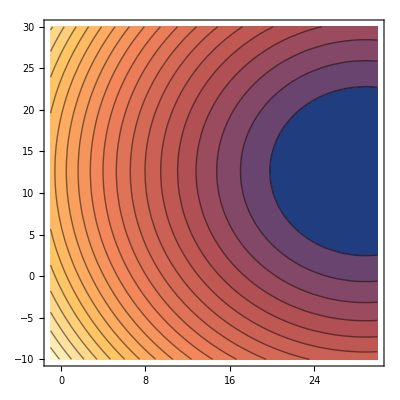

```mathematica
ContourPlot[Log[L], {γ,-1,30}, {ω,-10,30}, Contours->20]
```

```mathematica
Show[Plot3D[Log[L], {γ,-1,1}, {ω,-10,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PlotRange->All,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Show[Plot3D[Log[L], {γ,-1,1}, {ω,-10,30},
ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],
AxesLabel ->{γ,ω}],PlotRange->All,PerformanceGoal->"Quality"]
```

-Graphics3D-